```mathematica
data=Import["/home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p3.800_mu.100_0.nc","Data"]
```

Import::nffil: File /home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p3.800_mu.100_0.nc not found during Import.

$Failed

```mathematica
p0s=Table[p,{p,3.80,4.38,0.02}];
records={0,1};
```

```mathematica
timeEnergy=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p","_mu0.10_",".nc"},{p0s[[p]],records[[i]]},{3,0}],"Data"],{i,Length[records]}],{p,Length[p0s]}];
```

```mathematica
timeEnergy[[1,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
timeEnergyMean[[1,1]]
```

603.687

```mathematica
timeEnergyMean=Table[Table[Mean[Table[timeEnergy[[p,i,2,rec]],{i,Length[records]}]],{rec,Length[timeEnergy[[p,1,2]]]}],{p,Length[p0s]}];
```

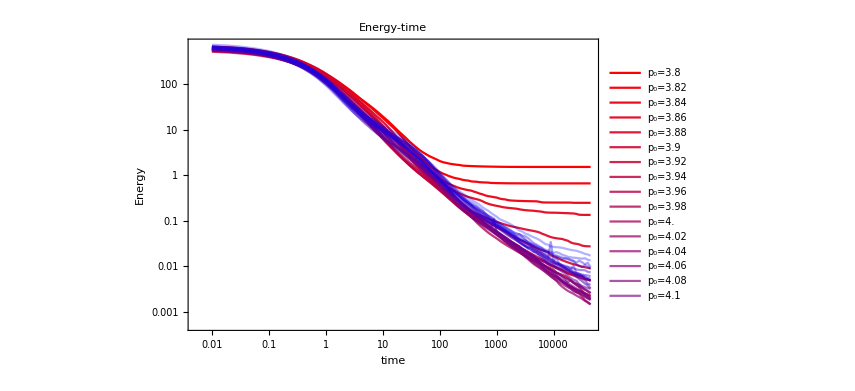

```mathematica
ListLogLogPlot[Table[Table[{timeEnergy[[p,1,1,rec]],timeEnergyMean[[p,rec]]},{rec,Length[timeEnergyMean[[p]]]}],{p,Length[p0s]}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"time","Energy"},ImageSize->600,PlotLabel->"Energy-time",Joined->True]
```

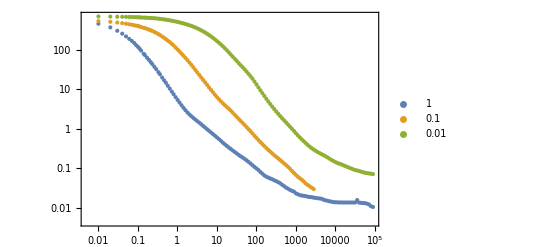

```mathematica
ListLogLogPlot[Table[Table[{timeEnergy[[mu,1,time]],timeEnergy[[mu,2,time]]},{time,Length[timeEnergy[[mu,1]]]}],{mu,3}],PlotLegends->{"1","0.1","0.01"}]
```

```mathematica
ListLogLogPlot[Table[Table[{timeEnergy[[mu,1,time]],timeEnergy[[mu,2,time]]},{time,Length[timeEnergy[[mu,1]]]}],{mu,3}],PlotLegends->{"1","0.1","0.01"}]
```

-Graphics-